# Wavepacket hitting a box Continued part 2

```mathematica
(*Here we now choose our solution that can be shown to come about.*)
x=.;
t=.;
a=.;
y=.;
V0=.;
α0=.;
x0=.;
k0=.;
hbar=.;
m=.;
n=(2Re[α]/π)^(1/4)*Exp[Im[I Log[((1+(2I hbar α)/m)^(1/2))]]];

γout=k0^2/(2m)t ;
γin=k0^2/(2m)t -V0 t;
α=α0/(1+(2I hbar α0 t/m));
p=hbar k0;
x=x0+hbar k0 t/m;
Ψin[y_,t_]:=n Exp[-α(y-x)^2+I/hbar p (y-x)+I/hbar γin]*(1+(2I hbar α)/m)^(-1/2)
Ψout[y_,t_]:=n Exp[-α(y-x)^2+I/hbar p (y-x)+I/hbar γout]*(1+(2I hbar α)/m)^(-1/2)
Ψin[y,t]
(*Where these are definied depending if we are inside or outside the potential which goes from 10-a to 10 and is a simple box potential.*)
(*Where this is now our full wavefunction which should be normalized.*)
```

(ⅇ^((ⅈ ((k0^2 t)/(2 m)-t V0))/hbar+ⅈ k0 (-(hbar k0 t)/m-x0+y)-((-(hbar k0 t)/m-x0+y)^2 α0)/(1+(2 ⅈ hbar t α0)/m)+Re[Log[√(1+(2 ⅈ hbar α0)/(m (1+(2 ⅈ hbar t α0)/m)))]]) (2/π)^(1/4) Re[α0/(1+(2 ⅈ hbar t α0)/m)]^(1/4))/(√(1+(2 ⅈ hbar α0)/(m (1+(2 ⅈ hbar t α0)/m))))

```mathematica
(*We now check this normalization first for arbitrary t and then for more suitable t*)
y=.;
t=.
a=5;
V0=-0.4;
α0=.1;
x0=15;
k0=-2;
hbar=1;
m=.5;
Ψin[y,t]*Conjugate[Ψin[y,t]];
Ψout[y,t]*Conjugate[Ψout[y,t]];
t=0;
Integrate[Ψout[y,t]*Conjugate[Ψout[y,t]],{y,-∞,∞}]
```

1.-1.10218×10^-14 ⅈ

```mathematica
t=0;
Integrate[Ψout[y,t]*Conjugate[Ψout[y,t]],{y,-∞,∞}]
t=4;
Integrate[Ψin[y,4]*Conjugate[Ψin[y,4]],{y,-∞,∞}]
```

1.-1.22473×10^-15 ⅈ

1.-6.06819×10^-15 ⅈ

```mathematica
(*Checking normality, since the potential is disregarded when we are working on the probability density we can just use Ψout instead of making a piecewise case*)
t=0;
Integrate[Ψout[y,t=1]*Conjugate[Ψout[y,t=1]],{y,-∞,∞}]
```

1.-3.42057×10^-15 ⅈ

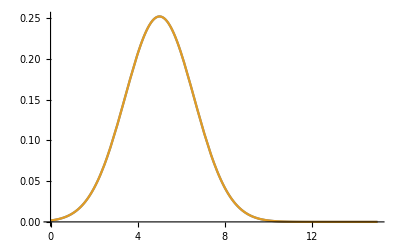

```mathematica
t=.;
Plot[{Piecewise[{{Ψout[y,t=0]*Conjugate[Ψout[y,t=0]],y<10-a},{Ψin[y,t=0]*Conjugate[Ψin[y,t=0]],10-a<=y<=10},{Ψout[y,t=0]*Conjugate[Ψout[y,t=0]],y>10}}],Ψout[y,t=0]*Conjugate[Ψout[y,t=0]]},{y,0,15}]
```

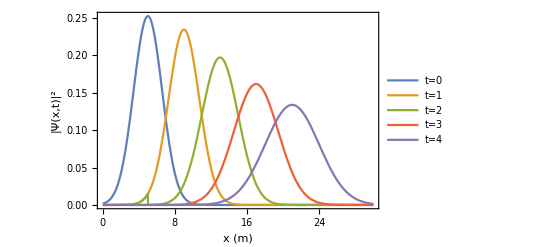

```mathematica
t=.;
Plot[{Piecewise[{{Ψout[y,t=0]*Conjugate[Ψout[y,t=0]],y<10-a},{Ψin[y,t=0]*Conjugate[Ψin[y,t=0]],10-a<=y<=10},{Ψout[y,t=0]*Conjugate[Ψout[y,t=0]],y>10}}],Piecewise[{{Ψout[y,t=1]*Conjugate[Ψout[y,t=1]],y<10-a},{Ψin[y,t=1]*Conjugate[Ψin[y,t=1]],10-a<=y<=10},{Ψout[y,t=1]*Conjugate[Ψout[y,t=1]],y>10}}],Piecewise[{{Ψout[y,t=1]*Conjugate[Ψout[y,t=1]],y<10-a},{Ψin[y,t=2]*Conjugate[Ψin[y,t=2]],10-a<=y<=10},{Ψout[y,t=2]*Conjugate[Ψout[y,t=2]],y>10}}],Piecewise[{{Ψout[y,t=3]*Conjugate[Ψout[y,t=3]],y<10-a},{Ψin[y,t=3]*Conjugate[Ψin[y,t=3]],10-a<=y<=10},{Ψout[y,t=3]*Conjugate[Ψout[y,t=3]],y>10}}],Piecewise[{{Ψout[y,t=4]*Conjugate[Ψout[y,t=4]],y<10-a},{Ψin[y,t=4]*Conjugate[Ψin[y,t=4]],10-a<=y<=10},{Ψout[y,t=4]*Conjugate[Ψout[y,t=4]],y>10}}]},{y,0,30},PlotRange->All,Frame->True,FrameLabel->{"x (m)","|Ψ(x,t)|^2","Probability Density of a Gaussian Wavepacket for different times"},PlotLegends->{"t=0","t=1","t=2","t=3","t=4"}]
```

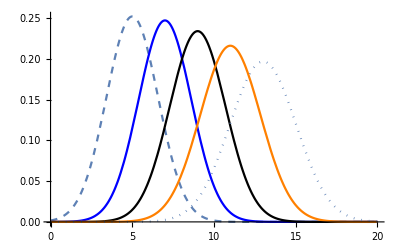

```mathematica
V0=-100000;
Show[Plot[Piecewise[{{Ψout[y,t=0]*Conjugate[Ψout[y,t=0]],y<10-a},{Ψin[y,t=0]*Conjugate[Ψin[y,t=0]],10-a<=y<=10},{Ψout[y,t=0]*Conjugate[Ψout[y,t=0]],y>10}}],{y,0,20},PlotStyle->Dashed],Plot[Piecewise[{{Ψout[y,t=.5]*Conjugate[Ψout[y,t=.5]],y<10-a},{Ψin[y,t=.5]*Conjugate[Ψin[y,t=.5]],10-a<=y<=10},{Ψout[y,t=.5]*Conjugate[Ψout[y,t=.5]],y>10}}],{y,0,20},PlotStyle->Blue],Plot[Piecewise[{{Ψout[y,t=1]*Conjugate[Ψout[y,t=1]],y<10-a},{Ψin[y,t=1]*Conjugate[Ψin[y,t=1]],10-a<=y<=10},{Ψout[y,t=1]*Conjugate[Ψout[y,t=1]],y>10}}],{y,0,20},PlotStyle->Black],Plot[Piecewise[{{Ψout[y,t=1.5]*Conjugate[Ψout[y,t=1.5]],y<10-a},{Ψin[y,t=1.5]*Conjugate[Ψin[y,t=1.5]],10-a<=y<=10},{Ψout[y,t=1.5]*Conjugate[Ψout[y,t=1.5]],y>10}}],{y,0,20},PlotStyle->Orange],Plot[Piecewise[{{Ψout[y,t=2]*Conjugate[Ψout[y,t=2]],y<10-a},{Ψin[y,t=2]*Conjugate[Ψin[y,t=2]],10-a<=y<=10},{Ψout[y,t=2]*Conjugate[Ψout[y,t=2]],y>10}}],{y,0,20},PlotStyle->Dotted],PlotRange->All]
```

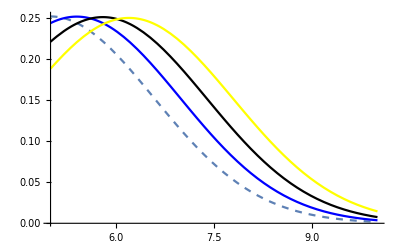

```mathematica
Show[Plot[Ψin[y,t=0]*Conjugate[Ψin[y,t=0]],{y,10-a,10},PlotStyle->Dashed],Plot[Ψin[y,t=.1]*Conjugate[Ψin[y,t=.1]],{y,10-a,10},PlotStyle->Blue],Plot[Ψin[y,t=.2]*Conjugate[Ψin[y,t=.2]],{y,10-a,10},PlotStyle->Black],Plot[Ψin[y,t=.3]*Conjugate[Ψin[y,t=.3]],{y,10-a,10},PlotStyle->Yellow],PlotRange->All]
```

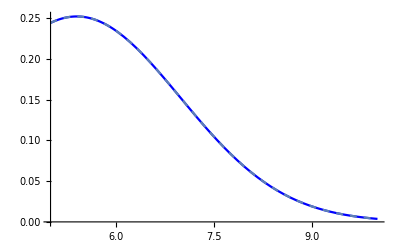

```mathematica
(*To see if the Box potential is actually making some sort of difference we can compare the in and out wavefunctions*)
(*Importantly we used a time other than t=0, since at this time the potential immediately diminishes to zero anyway.*)
V0=1;
Show[Plot[Ψin[y,t=.1]*Conjugate[Ψin[y,t=.1]],{y,5,10},PlotStyle->Blue],Plot[Ψout[y,t=.1]*Conjugate[Ψout[y,t=.1]],{y,5,10},PlotStyle->Dashed]]
```

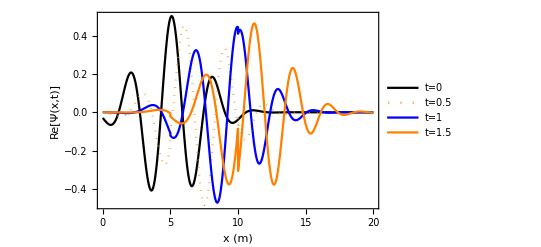

```mathematica
t=.;
V0=-.4;
Plot[{Piecewise[{{Re[Ψout[y,t=0]],y<10-a},{Re[Ψin[y,t=0]],10-a<=y<=10},{Re[Ψout[y,t=0]],y>10}}],Piecewise[{{Re[Ψout[y,t=.5]],y<10-a},{Re[Ψin[y,t=.5]],10-a<=y<=10},{Re[Ψout[y,t=.5]],y>10}}],Piecewise[{{Re[Ψout[y,t=1]],y<10-a},{Re[Ψin[y,t=1]],10-a<=y<=10},{Re[Ψout[y,t=1]],y>10}}],Piecewise[{{Re[Ψout[y,t=1.5]],y<10-a},{Re[Ψin[y,t=1.5]],10-a<=y<=10},{Re[Ψout[y,t=1.5]],y>10}}]},{y,0,20},PlotRange->All,Frame->True,PlotStyle->{Black,Dotted,Blue,Orange,Dots},FrameLabel->{"x (m)","Re[Ψ(x,t)]","Real Wavefunction of a Gaussian Wavepacket for different times V0=-0.4"},PlotLegends->{"t=0","t=0.5","t=1","t=1.5","t=2"}]
```

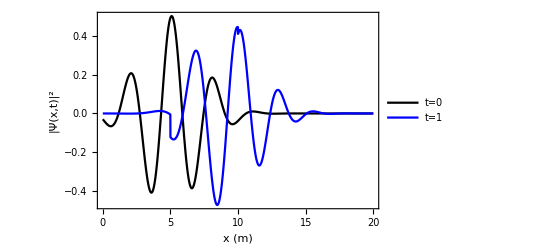

```mathematica
t=.;
Plot[{Piecewise[{{Re[Ψout[y,t=0]],y<10-a},{Re[Ψin[y,t=0]],10-a<=y<=10},{Re[Ψout[y,t=0]],y>10}}],Piecewise[{{Re[Ψout[y,t=1.5]],y<10-a},{Re[Ψin[y,t=1]],10-a<=y<=10},{Re[Ψout[y,t=1]],y>10}}]},{y,0,20},PlotRange->All,Frame->True,PlotStyle->{Black,Blue},FrameLabel->{"x (m)","|Ψ(x,t)|^2","Real Wavefunction of a Gaussian Wavepacket for different times"},PlotLegends->{"t=0","t=1"}]
```

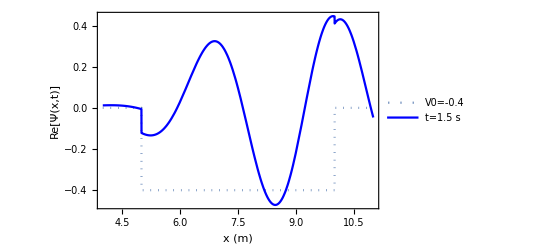

```mathematica
(*Here we look to show the discontinuity at the boundary of the potential, with the potential also shown on the graph for obviousness.*)
t=.;
V0=-.4;
Plot[{Piecewise[{{V0,10-a<=y<=10},{0,y<10-a},{0,y>10}}],Piecewise[{{Re[Ψout[y,t=1.5]],y<10-a},{Re[Ψin[y,t=1]],10-a<=y<=10},{Re[Ψout[y,t=1]],y>10},{Re[Ψout[y,t=1]],y<10-a}}]},{y,4,11},PlotRange->All,Frame->True,PlotStyle->{Dotted,Blue},FrameLabel->{"x (m)","Re[Ψ(x,t)]","Real Wavefunction of a Gaussian Wavepacket for different times"},PlotLegends->{"V0=-0.4","t=1.5 s"}]
```

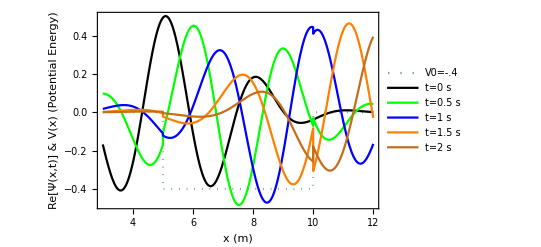

```mathematica
(*We can specifically look at the area inside the box to see how this if effected*)
t=.;
Plot[{Piecewise[{{V0,10-a<=y<=10},{0,y<10-a},{0,y>10}}],Piecewise[{{Re[Ψout[y,t=0]],y<10-a},{Re[Ψin[y,t=0]],10-a<=y<=10},{Re[Ψout[y,t=0]],y>10}}],Piecewise[{{Re[Ψout[y,t=.5]],y<10-a},{Re[Ψin[y,t=.5]],10-a<=y<=10},{Re[Ψout[y,t=.5]],y>10}}],Piecewise[{{Re[Ψout[y,t=1]],y<10-a},{Re[Ψin[y,t=1]],10-a<=y<=10},{Re[Ψout[y,t=1]],y>10}}],Piecewise[{{Re[Ψout[y,t=1.5]],y<10-a},{Re[Ψin[y,t=1.5]],10-a<=y<=10},{Re[Ψout[y,t=1.5]],y>10}}],Piecewise[{{Re[Ψout[y,t=2]],y<10-a},{Re[Ψin[y,t=2]],10-a<=y<=10},{Re[Ψout[y,t=2]],y>10}}]},{y,3,12},PlotRange->All,Frame->True,PlotStyle->{Dotted,Black,Green,Blue,Orange,Dots},FrameLabel->{"x (m)","Re[Ψ(x,t)] & V(x) (Potential Energy)","Real Wavefunction for the Gaussian Wavepacket for different times"},PlotLegends->{"V0=-.4","t=0 s","t=0.5 s","t=1 s","t=1.5 s","t=2 s"}]
```

```mathematica
(*We could also look at how the two different functions change inside the box. We skip over t=0, since there is no difference in wavefunctions, since the time dependence is linear with the constant potential.*)
```

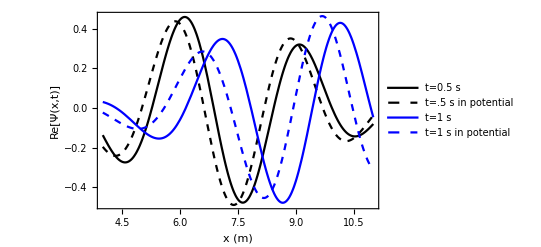

```mathematica
V0=-1;
Plot[{Re[Ψout[y,t=0.5]],Re[Ψin[y,t=0.5]],Re[Ψout[y,t=1]],Re[Ψin[y,t=1]]},{y,4,11}, PlotRange->All, PlotStyle->{{Black},{Black, Dashed},{Blue},{Blue,Dashed},{Orange},{Orange, Dashed},{Gray},{Gray,Dashed}},Frame->True,FrameLabel->{"x (m)","Re[Ψ(x,t)]","Real Wavefunction with and without the potential V0=1"},PlotLegends->{"t=0.5 s","t=.5 s in potential","t=1 s","t=1 s in potential"}]
```

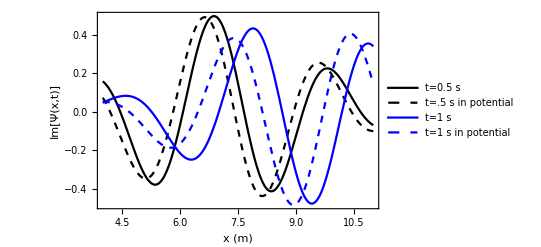

```mathematica
Plot[{Im[Ψout[y,t=0.5]],Im[Ψin[y,t=0.5]],Im[Ψout[y,t=1]],Im[Ψin[y,t=1]]},{y,4,11}, PlotRange->All, PlotStyle->{{Black},{Black, Dashed},{Blue},{Blue,Dashed},{Orange},{Orange, Dashed},{Gray},{Gray,Dashed}},Frame->True,FrameLabel->{"x (m)","Im[Ψ(x,t)]","Imaginary Wavefunction with and without the potential V0=1"},PlotLegends->{"t=0.5 s","t=.5 s in potential","t=1 s","t=1 s in potential"}]
```

```mathematica
(*We still must the the conservation of mean energy, meaning that the potential and kinetic energies must sum to a constant value for any time, so we will need to look at this and make sure it is sill the case.*)
(*Is this not already assumed by using the schrodinger equation?  I thought that this was specifically satisfied by implementing the Schrodinger equation, since this is an equation of the conservation of energy.*)
```

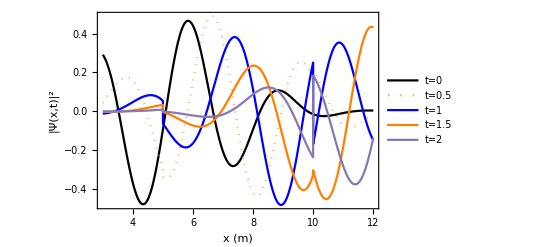

```mathematica
(*Here we have the imaginary parts of the wavefunctions as well*)
t=.;
Plot[{Piecewise[{{Im[Ψout[y,t=0]],y<10-a},{Im[Ψin[y,t=0]],10-a<=y<=10},{Im[Ψout[y,t=0]],y>10}}],Piecewise[{{Im[Ψout[y,t=.5]],y<10-a},{Im[Ψin[y,t=.5]],10-a<=y<=10},{Im[Ψout[y,t=.5]],y>10}}],Piecewise[{{Im[Ψout[y,t=1]],y<10-a},{Im[Ψin[y,t=1]],10-a<=y<=10},{Im[Ψout[y,t=1]],y>10}}],Piecewise[{{Im[Ψout[y,t=1.5]],y<10-a},{Im[Ψin[y,t=1.5]],10-a<=y<=10},{Im[Ψout[y,t=1.5]],y>10}}],Piecewise[{{Im[Ψout[y,t=2]],y<10-a},{Im[Ψin[y,t=2]],10-a<=y<=10},{Im[Ψout[y,t=2]],y>10}}]},{y,3,12},PlotRange->All,Frame->True,PlotStyle->{Black,Dotted,Blue,Orange,Dots},FrameLabel->{"x (m)","|Ψ(x,t)|^2","Imaginary wavefunction of a Gaussian Wavepacket for different times"},PlotLegends->{"t=0","t=0.5","t=1","t=1.5","t=2"}]
```

```mathematica
t=.;
D[D[Ψout[y,t],y],y]*(-hbar^2/2m)==I hbar D[Ψout[y,t],t]
```

-0.25 (-(0.100462 ⅇ^((0.+4. ⅈ) t+2 ⅈ (-5-4. t+y)-(0.1 (-5-4. t+y)^2)/(1+(0.+0.4 ⅈ) t)+Re[Log[√(1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t))]]) Re[1/(1+(0.+0.4 ⅈ) t)]^(1/4))/(√(1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t)) (1+(0.+0.4 ⅈ) t))+(0.502308 ⅇ^((0.+4. ⅈ) t+2 ⅈ (-5-4. t+y)-(0.1 (-5-4. t+y)^2)/(1+(0.+0.4 ⅈ) t)+Re[Log[√(1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t))]]) (2 ⅈ-(0.2 (-5-4. t+y))/(1+(0.+0.4 ⅈ) t))^2 Re[1/(1+(0.+0.4 ⅈ) t)]^(1/4))/(√(1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t))))==ⅈ (-((0.0401846+0. ⅈ) ⅇ^((0.+4. ⅈ) t+2 ⅈ (-5-4. t+y)-(0.1 (-5-4. t+y)^2)/(1+(0.+0.4 ⅈ) t)+Re[Log[√(1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t))]]) Re[1/(1+(0.+0.4 ⅈ) t)]^(1/4))/((1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t))^(3/2) (1+(0.+0.4 ⅈ) t)^2)-((0.+0.0502308 ⅈ) ⅇ^((0.+4. ⅈ) t+2 ⅈ (-5-4. t+y)-(0.1 (-5-4. t+y)^2)/(1+(0.+0.4 ⅈ) t)+Re[Log[√(1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t))]]) Re'[1/(1+(0.+0.4 ⅈ) t)])/(√(1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t)) (1+(0.+0.4 ⅈ) t)^2 Re[1/(1+(0.+0.4 ⅈ) t)]^(3/4))+1/(√(1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t)))0.502308 ⅇ^((0.+4. ⅈ) t+2 ⅈ (-5-4. t+y)-(0.1 (-5-4. t+y)^2)/(1+(0.+0.4 ⅈ) t)+Re[Log[√(1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t))]]) Re[1/(1+(0.+0.4 ⅈ) t)]^(1/4) ((0.-4. ⅈ)+(0.8 (-5-4. t+y))/(1+(0.+0.4 ⅈ) t)+((0.+0.04 ⅈ) (-5-4. t+y)^2)/(1+(0.+0.4 ⅈ) t)^2+((0.08+0. ⅈ) Re'[Log[√(1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t))]])/((1+(0.+0.4 ⅈ)/(1+(0.+0.4 ⅈ) t)) (1+(0.+0.4 ⅈ) t)^2)))

```mathematica
t=.;
totalEout[y_,t_]=I hbar D[Ψout[y,t],t];
kineticEout[y_,t_]=D[D[Ψout[y,t],y],y]*(-hbar^2/2m);
totalEin[y_,t_]=I hbar D[Ψin[y,t],t];
kineticEin[y_,t_]=D[D[Ψin[y,t],y],y]*(-hbar^2/2m);
```

```mathematica
(*t=.;
D[Integrate[Ψout[y,t]*totalEout[y,t]*Conjugate[Ψout[y,t]],{y,-10,10}],t]
```

$Aborted

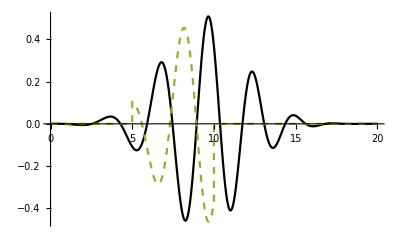

```mathematica
(*Maybe instead of actually finding a constant we graph the potential and Kinetic energies of the system and see how it compares with the total energy of the system*)
t=1;
y=.;
Plot[{Re[kineticEin[y,t=1]],Evaluate[Re[totalEin[y,t=1]]],Piecewise[{{0,y<10-a},{V0 Re[Ψin[y,t]],10-a<=y<=10},{0,y>10}}]},{y,0,20},PlotRange->All,PlotStyle->{Black,Blue,Dashed}]
```

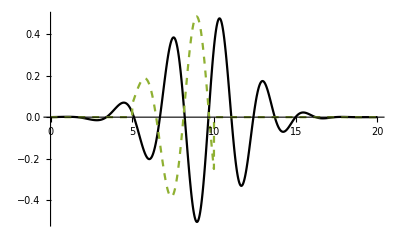

```mathematica
t=1;
y=.;
Plot[{Im[kineticEin[y,t=1]],Im[totalEin[y,t=1]],Piecewise[{{0,y<10-a},{V0 Im[Ψin[y,t]],10-a<=y<=10},{0,y>10}}]},{y,0,20},PlotRange->All,PlotStyle->{Black,Blue,Dashed}]
```

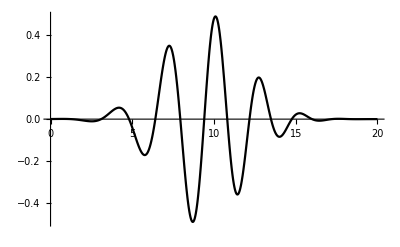

```mathematica
t=1;
y=.;
Plot[{Re[kineticEout[y,t=1]],Re[totalEout[y,t=1]]},{y,0,20},PlotRange->All,PlotStyle->{Black,Blue,Dashed}]
```